# Projeto Computacional de Oscilações e Ondas

## Obtenção de modos e frequências normais e plot de gráficos

## Duarte Marques, ist196253

## Cálculo dos valores próprios

Seja (a | b | c
d | e | f
g | h | i)  a matriz cujo determinante se pretende determinar. De acordo com as informações apresentadas no trabalho, os elementos da matriz são os apresentados de seguida.

```mathematica
a=-w^2+ⅈ*w+1+1+1
```

3+ⅈ w-w^2

```mathematica
b=-1
```

-1

```mathematica
c=-1
```

-1

```mathematica
d=-1
```

-1

```mathematica
e=-w^2+ⅈ*w+1+1
```

2+ⅈ w-w^2

```mathematica
f=-ⅈ*w-1
```

-1-ⅈ w

```mathematica
g=-1
```

-1

```mathematica
h=-ⅈ*w-1
```

-1-ⅈ w

```mathematica
j=ⅈ*w+1+1
```

2+ⅈ w

Em seguida, determinam-se os valores próprios da matriz, igualando a expressão do respetivo determinante (obtida pela Regra de Sarrus) a zero.

```mathematica
sol=Solve[a*e*j+b*f*g+c*d*h-c*e*g-a*f*h-b*d*j==0,w]
```

{{w→Root-1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,1}]-1.9425189204581643},{w→Root-0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,2}]-0.6399670863355232},{w→Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.},{w→Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232},{w→Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643}}

Apresentam-se, agora, os valores obtidos numa forma mais clara:

```mathematica
N[sol]
```

{{w→-1.94252+0.467801 ⅈ},{w→-0.639967+0.186864 ⅈ},{w→0.+1.69067 ⅈ},{w→0.639967+0.186864 ⅈ},{w→1.94252+0.467801 ⅈ}}

Atribuir os valores próprios que se irão analisar a variáveis w1, w2 e w3:

```mathematica
w1=w/.sol[[3]]
```

Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.

```mathematica
w2=w/.sol[[4]]
```

Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232

```mathematica
w3=w/.sol[[5]]
```

Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643

## Determinação dos vetores próprios

Resolver o sistema de equações para determinação dos valores próprios  (a1
a2
a3) :

```mathematica
Solve[{a1*(-w1^2+ⅈ*w1+3)-a2-a3==0,-a1+a2*(-w1^2+ⅈ*w1+2)+a3*(-ⅈ*w1-1)==0,-a1+a2*(-ⅈ*w1-1)+a3*(ⅈ*w1+2)==0},{a1,a2,a3}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{a2→-(a1 (5 ⅈ-5 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.-3 ⅈ (Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^2+(Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^3))/(-3 ⅈ+2 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.),a3→-(a1 (4 ⅈ-4 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.-2 ⅈ (Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^2+(Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^3))/(-3 ⅈ+2 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)}}

Definir variáveis contendo os elementos do vetor próprio (a1w1
a2w1
a3w1) correspondente ao valor próprio w1:

```mathematica
a1w1=1
```

1

```mathematica
a2w1=(5*ⅈ-5*w1-3*ⅈ*w1^2+w1^3)/(3*ⅈ-2*w1)
```

(5 ⅈ-5 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.-3 ⅈ (Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^2+(Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^3)/(3 ⅈ-2 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)

```mathematica
a3w1=(4*ⅈ-4*w1-2*ⅈ*w1^2+w1^3)/(3*ⅈ-2*w1)
```

(4 ⅈ-4 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.-2 ⅈ (Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^2+(Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)^3)/(3 ⅈ-2 Root1.69 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,3}]0.)

Para o vetor próprio (a1w2
a2w2
a3w2) , do valor próprio w2:

```mathematica
a1w2=1
```

1

```mathematica
a2w2=(5*ⅈ-5*w2-3*ⅈ*w2^2+w2^3)/(3*ⅈ-2*w2)
```

(5 ⅈ-5 Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232-3 ⅈ (Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)^2+(Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)^3)/(3 ⅈ-2 Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)

```mathematica
a3w2=(4*ⅈ-4*w2-2*ⅈ*w2^2+w2^3)/(3*ⅈ-2*w2)
```

(4 ⅈ-4 Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232-2 ⅈ (Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)^2+(Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)^3)/(3 ⅈ-2 Root0.640+0.187 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,4}]0.6399670863355232)

E, por fim, para o valor próprio w3, tem-se o vetor próprio (a1w3
a2w3
a3w3) :

```mathematica
a1w3=1
```

1

```mathematica
a2w3=(5*ⅈ-5*w3-3*ⅈ*w3^2+w3^3)/(3*ⅈ-2*w3)
```

(5 ⅈ-5 Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643-3 ⅈ (Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)^2+(Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)^3)/(3 ⅈ-2 Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)

```mathematica
a3w3=(4*ⅈ-4*w3-2*ⅈ*w3^2+w3^3)/(3*ⅈ-2*w3)
```

(4 ⅈ-4 Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643-2 ⅈ (Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)^2+(Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)^3)/(3 ⅈ-2 Root1.94+0.468 ⅈRoot[{1+#1^2&,3+5 #1 #2-10 #2^2-7 #1 #2^3+3 #2^4+#1 #2^5&},{2,5}]1.9425189204581643)

## Desenho dos gráficos relativos aos movimentos das massas para cada frequência normal

#### Frequência normal w1

Parte real

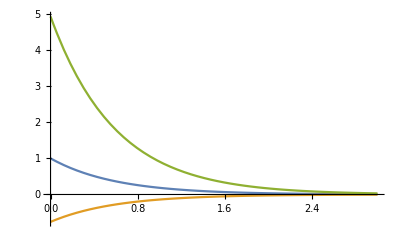

```mathematica
Plot[{Re[ⅇ^(ⅈ*w1*t)],Re[a2*ⅇ^(ⅈ*w1*t)],Re[a3*ⅇ^(ⅈ*w1*t)]},{t,0,3},PlotRange->Full]
```

Parte imaginária

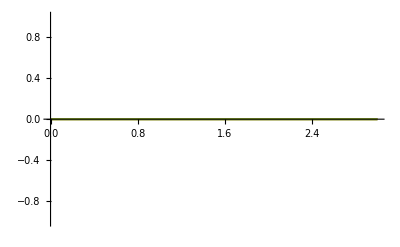

```mathematica
Plot[{Im[ⅇ^(ⅈ*w1*t)],Im[a2*ⅇ^(ⅈ*w1*t)],Im[a3*ⅇ^(ⅈ*w1*t)]},{t,0,3},PlotRange->Full]
```

#### Frequência normal w2

Parte real

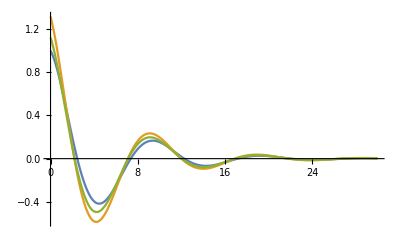

```mathematica
Plot[{Re[ⅇ^(ⅈ*w2*t)],Re[b2*ⅇ^(ⅈ*w2*t)],Re[b3*ⅇ^(ⅈ*w2*t)]},{t,0,30},PlotRange->Full]
```

Parte imaginária

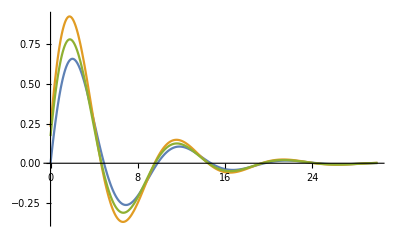

```mathematica
Plot[{Im[ⅇ^(ⅈ*w2*t)],Im[b2*ⅇ^(ⅈ*w2*t)],Im[b3*ⅇ^(ⅈ*w2*t)]},{t,0,30},PlotRange->Full]
```

#### Frequência normal w3

Parte real

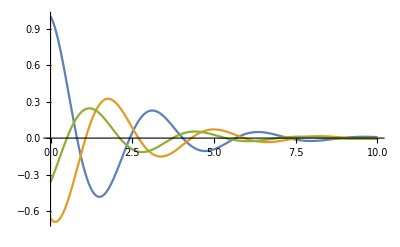

```mathematica
Plot[{Re[ⅇ^(ⅈ*w3*t)],Re[c2*ⅇ^(ⅈ*w3*t)],Re[c3*ⅇ^(ⅈ*w3*t)]},{t,0,10},PlotRange->Full]
```

Parte imaginária

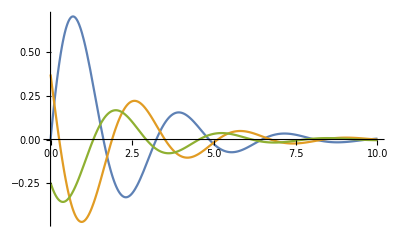

```mathematica
Plot[{Im[ⅇ^(ⅈ*w3*t)],Im[c2*ⅇ^(ⅈ*w3*t)],Im[c3*ⅇ^(ⅈ*w3*t)]},{t,0,10},PlotRange->Full]
```